```mathematica
NS["plinkinetti_3Dvis"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\matches_3_parameters\\saved_data\\"
```

C:\Users\pglpm\repositories\plinkinetti\matches_3_parameters\saved_data\

```mathematica
logt[x_,a_:1]=Sign[x]*Log[10,1+Abs[x/a]];
ilogt[x_,a_:1]=Sign[x]*(10^(Abs[x/a])-1);
```

```mathematica
pairs=Flatten[Table[{i,j},{i,1,3},{j,i+1,3}],1];npairs=Length[pairs];
names={"intercept","m coeff","s coeff"};
```

```mathematica
data=Import[wd<>"points_kl1mean.csv"];data[[1;;3]]
```

{{1,-99.1212,2.88446,-100.828},{2,2.47749,-1.46641,-3.3745},{3,-14.7177,-1.41591,13.4986}}

```mathematica
data=Delete[10]@data;
```

```mathematica
myfontsize=15;tab=Table[
plot[i]=Show[{ListPlot[data[[;;,pairs[[i]]+1]],PlotRange->Table[{-50,50},2],
PlotMarkers->{"+",Large},FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->"Palatino"],AspectRatio->1,
Axes->None,Frame->{True,True,False,False},FrameLabel->myaxes[names[[pairs[[i]]]]]],Graphics[Text[#[[1]],#[[pairs[[i]]+1]]]&/@data]}]
,{i,npairs}];
```

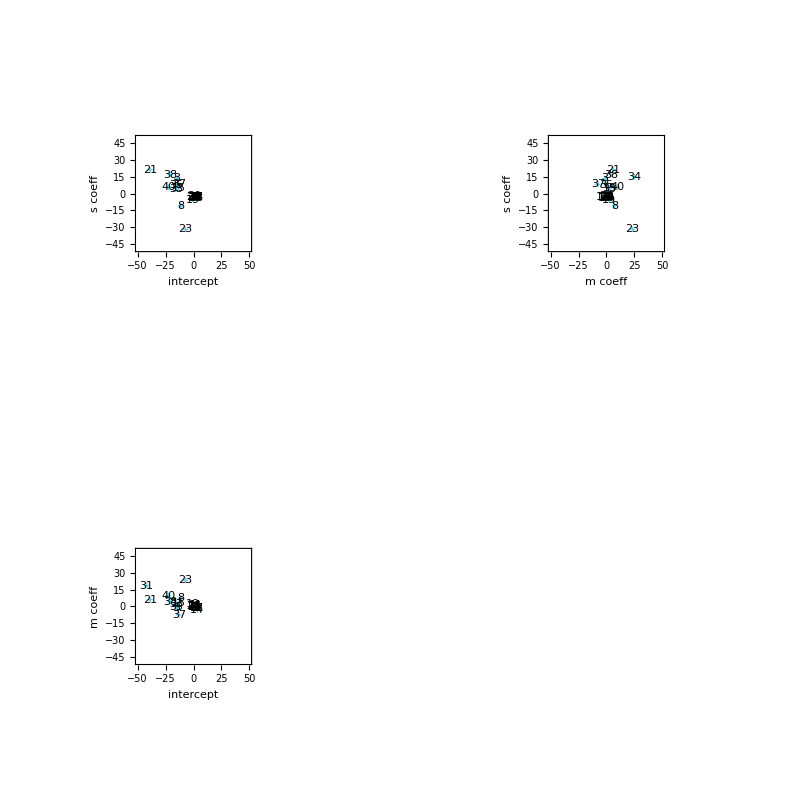

```mathematica
GraphicsGrid[{{plot[2],plot[3]},{plot[1],""}},Spacings->Auto]
```

```mathematica
expng[wd<>"kl1mean_zoom"]
```

C:\Users\pglpm\repositories\plinkinetti\matches_3_parameters\saved_data\kl1mean_zoom.png

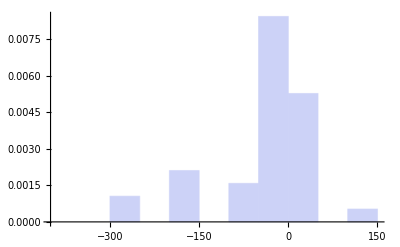

```mathematica
Histogram[data[[;;,2]],"FreedmanDiaconis","PDF",PlotRange->Auto]
```

```mathematica
ListPointPlot3D[data[[;;,2;;4]],BoxRatios->1,PlotStyle->PointSize[Large],PlotLabel->mylabels[{"JS-mean"}],ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
expdf["plot_JS-mean"]
```

plot_JS-mean.pdf

```mathematica
data=Import[wd<>"points_js1mean.csv"];
```

```mathematica
data=Delete[10]@data;
```

```mathematica
data[[10,2;;4]]//MF
```

(Infinity
10
Infinity)

```mathematica
plot=ListPointPlot3D[data[[;;,2;;4]],BoxRatios->1,PlotStyle->PointSize[0.02],PlotLabel->mylabels[{"JS-mean"}],ViewPoint->Dynamic[viewpoint],PlotRange->All,AxesLabel->myaxes[{"intercept","m coeff","s coeff"}]];
```

```mathematica
Show[plot,Graphics3D[Text[#[[1]],1.04 #[[2;;4]]]&/@data]]
```

-Graphics3D-

```mathematica
expdf["plot_JS-mean"]
```

plot_JS-mean.pdf